{a1→0.112834,b1→-0.5,c1→1.63067}

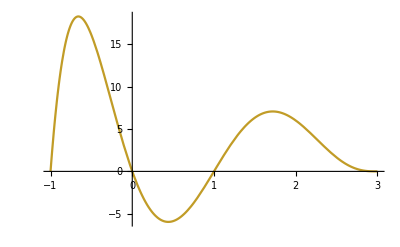

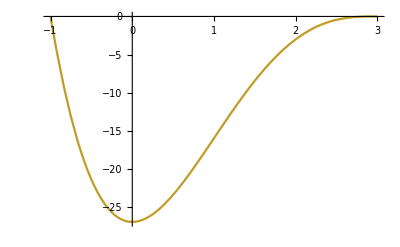

```mathematica
sol2//N
Plot[-(x+1)x(x-1)(x-3)^3,{x,-1,3}]
Plot[(x+1)(x-3)^3,{x,-1,3}]
```

```mathematica
Plot[(x+1)x(x-1)(x-5),{x,-1,5}]
```

```mathematica
g=-(x+1)x(x-1)(x-3)^3;
```

```mathematica
f=x(x-1);
DorisAlgorithmCompactCase[x,f,{g}]
```

```mathematica
Series[1+(a1^2(x-b1)^2+c1^2)((a2^2(x-b2)^2+c2^2))(x+1)(x-3),{x,0,10}]
Series[1+(a1^2(x-b1)^2+c1^2)((a2^2(x-b2)^2+c2^2))(x+1)(x-3),{x,1,10}]
```

```mathematica
sol1=FindInstance[(1-3 (a1^2 b1^2+c1^2) (a2^2 b2^2+c2^2))==0&&(1-4 (a1^2 (-1+b1)^2+c1^2) (a2^2 (-1+b2)^2+c2^2))==0,{a1,b1,c1,a2,b2,c2},Reals][[1]]
```

```mathematica
Series[1+a1^2((x-b1)^2+c1^2)(x+1)(x-3)^3,{x,0,10}]
Series[1+a1^2((x-b1)^2+c1^2)(x+1)(x-3)^3,{x,1,10}]
```

(1-27 a1^2 (b1^2+c1^2))+54 a1^2 b1 x+a1^2 (-27+18 (b1^2+c1^2)) x^2+a1^2 (-36 b1-8 (b1^2+c1^2)) x^3+a1^2 (18+16 b1+b1^2+c1^2) x^4+a1^2 (-8-2 b1) x^5+a1^2 x^6+O[x]^11

(1-16 a1^2 ((1-b1)^2+c1^2))+16 a1^2 (-1+b1^2+c1^2) (x-1)-16 (a1^2 (-1+2 b1)) (x-1)^2+a1^2 (16-4 ((1-b1)^2+c1^2)) (x-1)^3+a1^2 (-4 (2-2 b1)+(1-b1)^2+c1^2) (x-1)^4+a1^2 (-2-2 b1) (x-1)^5+a1^2 (x-1)^6+O[x-1]^11

```mathematica
sol2=FindInstance[(1-27 a1^2 (b1^2+c1^2))==0&&(1-16 a1^2 ((1-b1)^2+c1^2))==0&&54 a1^2 b1 ≤0&&16 a1^2 (-1+b1^2+c1^2)≥0&&-1≤b1≤3,{a1,b1,c1},Reals][[1]]
```

{a1→(√(11/6))/12,b1→-1/2,c1→(3 √(13/11))/2}

```mathematica
s1=a1^2((x-b1)^2+c1^2)/.sol2;
F2=1+s1 (x+1)(x-3)^3;
s0=f F2;
Reduce[s1<0,x]
Reduce[s0<0,x]
s0+s1 (g)//Simplify
```

False

False

(-1+x) x

{a1→0.112834,b1→-0.5,c1→1.63067}

-Graphics-

-Graphics-

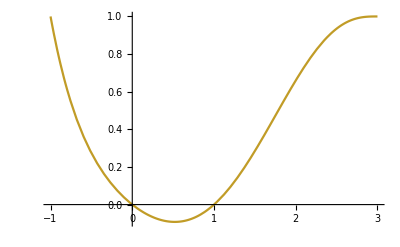

```mathematica
sol2//N
Plot[-(x+1)x(x-1)(x-3)^3,{x,-1,3}]
Plot[(x+1)(x-3)^3,{x,-1,3}]
Plot[F2,{x,-1,3}]
```